## Truncated NFW halo Fourier NFW halo CS02 at |k|=0

```mathematica
Sin[x]* (SinIntegral[(1+c)*x]-SinIntegral[x])-Sin[c*x]/(1+c)/x+Cos[x]*(CosIntegral[(1+c)*x]-CosIntegral[x])
```

Cos[x] (-CosIntegral[x]+CosIntegral[(1+c) x])-Sin[c x]/((1+c) x)+Sin[x] (-SinIntegral[x]+SinIntegral[(1+c) x])

```mathematica
Series[Sin[x]* (SinIntegral[(1+c)*x]-SinIntegral[x])-Sin[c*x]/(1+c)/x+Cos[x]*(CosIntegral[(1+c)*x]-CosIntegral[x]),{x,0,2}]
```

Floor[(π-Arg[1+c]-Arg[x])/(2 π)] (2 ⅈ π-ⅈ π x^2+O[x]^3)+((-c/(1+c)+Log[1+c])+(c+c^3/(6 (1+c))+1/4 (-2 c-c^2-2 Log[1+c])) x^2+O[x]^3)

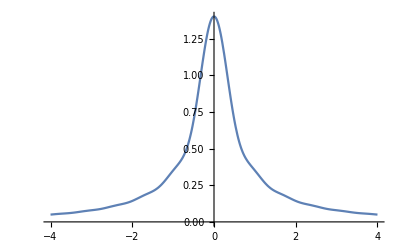

```mathematica
c:=9
Plot[Sin[x]* (SinIntegral[(1+c)*x]-SinIntegral[x])-Sin[c*x]/(1+c)/x+Cos[x]*(CosIntegral[(1+c)*x]-CosIntegral[x]),{x,-4,4}]
```

## ArcCosh and ArcTanh..

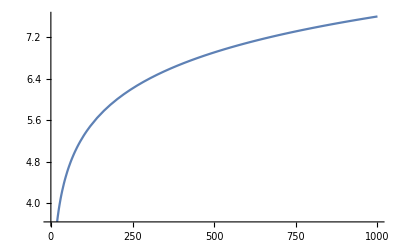

```mathematica
Plot[ArcCosh[x],{x,-1,1000}]
```

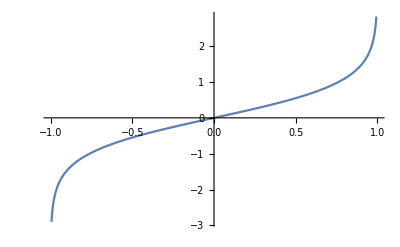

```mathematica
Plot[ArcTanh[x],{x,-1,1}]
```

## NFW halo TJ03 Surface Density (TJ03b)

```mathematica
Clear[c]
f1:= -Sqrt[c^2-x^2]/(1-x^2)/(1+c)+ArcCosh[(x^2+c)/x/(1+c)]/(1-x^2)^(3/2)
```

```mathematica
f1
```

-(√(c^2-x^2))/((1+c) (1-x^2))+ArcCosh[(c+x^2)/((1+c) x)]/((1-x^2)^(3/2))

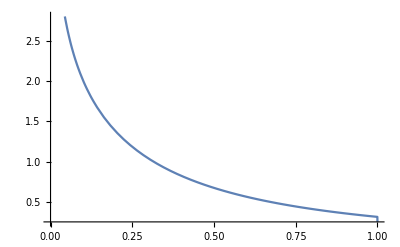

```mathematica
c:=4.
Plot[f1,{x,0,1.}]
```

```mathematica
Simplify[Expand[Series[f1,{x,1,1}]],Arg[c]==0&&Arg[x]==0 && Arg[x-c]==0 && x<1 ]
```

(-ⅈ √((1-c)/(1+c))+(√(-1+c^2))/(1+c))/(2 (x-1))+(-2+c+c^2)/(3 (1+c) √(-1+c^2))+((2-5 c+5 c^3-2 c^5) (x-1))/(5 (-1+c^2)^(5/2))+O[x-1]^2

```mathematica
Element[x,Reals]
Clear[c]
f2:= -Sqrt[c^2-x^2]/(1-x^2)/(1+c)-ArcCos[(x^2+c)/x/(1+c)]/(x^2-1)^(3/2)
```

```mathematica
f2
```

-(√(c^2-x^2))/((1+c) (1-x^2))-ArcCos[(c+x^2)/((1+c) x)]/((-1+x^2)^(3/2))

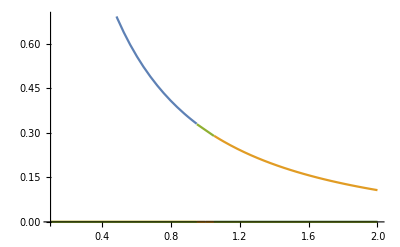

```mathematica
c:=4
p[x_,left_,right_]:=HeavisideTheta[x-left] HeavisideTheta[right-x]
f3:=(-2+c+c^2)/(3 √(-1+c) (1+c)^(3/2))+((2-c-4 c^2-2 c^3) (x-1))/(5 √(-1+c) (1+c)^(5/2))
Plot[{f1 p[x,0.1,0.95],f2 p[x,1.05,2],f3 p[x,0.95,1.05] },{x,0.1,2}]
```

```mathematica
Clear[c]
Simplify[Series[f2,{x,1,1}],Arg[c]==0&&Arg[x]==0 && Arg[c-x]==0]
```

(-2+c+c^2)/(3 √(-1+c) (1+c)^(3/2))+((2-c-4 c^2-2 c^3) (x-1))/(5 √(-1+c) (1+c)^(5/2))+O[x-1]^2

## Excess Surface Density (TJ03c)

```mathematica
Clear[c,f1,f2,f3]
```

```mathematica
f1:= 1/x^2/(1+c)((2-x^2)*Sqrt[c^2-x^2]/(1-x^2)-2c)+2/x^2 *Log[x*(1+c)/(c+Sqrt[c^2-x^2])]+(2-3x^2)/x^2/(1-x^2)^(3/2) ArcCosh[(x^2+c)/x/(1+c)]
f1
```

(-8+((2-x^2) √(16-x^2))/(1-x^2))/(5 x^2)+((2-3 x^2) ArcCosh[(4+x^2)/(5 x)])/(x^2 (1-x^2)^(3/2))+(2 Log[(5 x)/(4+√(16-x^2))])/x^2

```mathematica
FullSimplify[Series[f1,{x,1,1}],Arg[c]==0&&Arg[x]==0 && Arg[x-c]==0&&c>1]
```

(10 √(-1+c^2)+c (-6-6 c+11 √(-1+c^2))+6 (1+c)^2 Log[(1+c)/(c+√(-1+c^2))])/(3 (1+c)^2)+((94+c (113+60 √((-1+c)/(1+c))+4 c (-22+30 √((-1+c)/(1+c))+c (-26+15 √((-1+c)/(1+c))))))/(15 (1+c)^2 √(-1+c^2))-4 Log[1+c]+4 Log[c+√(-1+c^2)]) (x-1)+O[x-1]^2

```mathematica
f2:= 1/x^2/(1+c)((2-x^2)*Sqrt[c^2-x^2]/(1-x^2)-2c)+2/x^2 *Log[x*(1+c)/(c+Sqrt[c^2-x^2])]-(2-3x^2)/x^2/(x^2-1)^(3/2) ArcCos[(x^2+c)/x/(1+c)]
f2
```

(-8+((2-x^2) √(16-x^2))/(1-x^2))/(5 x^2)-((2-3 x^2) ArcCos[(4+x^2)/(5 x)])/(x^2 (-1+x^2)^(3/2))+(2 Log[(5 x)/(4+√(16-x^2))])/x^2

```mathematica
FullSimplify[Series[f2,{x,1,1}],Arg[c]==0&&Arg[x]==0 && Arg[x-c]==0 && c>1 ]
```

(10 √(-1+c^2)+c (-6-6 c+11 √(-1+c^2))+6 (1+c)^2 Log[(1+c)/(c+√(-1+c^2))])/(3 (1+c)^2)+((94+c (113+60 √((-1+c)/(1+c))+4 c (-22+30 √((-1+c)/(1+c))+c (-26+15 √((-1+c)/(1+c))))))/(15 (1+c)^2 √(-1+c^2))-4 Log[1+c]+4 Log[c+√(-1+c^2)]) (x-1)+O[x-1]^2

```mathematica
(-8/5+(18 √(3/5))/5+Log[25 (-4+√15)^2])+(16/5-2506/(125 √15)+Log[1/(625 (-4+√15)^4)]) (x-1)+O[x-1]^(3/2)
f3:=(10 √(-1+c^2)+c (-6-6 c+11 √(-1+c^2))+6 (1+c)^2 Log[(1+c)/(c+√(-1+c^2))])/(3 (1+c)^2)+((94+c (113+60 √((-1+c)/(1+c))+4 c (-22+30 √((-1+c)/(1+c))+c (-26+15 √((-1+c)/(1+c))))))/(15 (1+c)^2 √(-1+c^2))-4 Log[1+c]+4 Log[c+√(-1+c^2)]) (x-1)
```

(-8/5+(18 √(3/5))/5+Log[25 (-4+√15)^2])+(16/5-2506/(125 √15)+Log[1/(625 (-4+√15)^4)]) (x-1)+O[x-1]^(3/2)

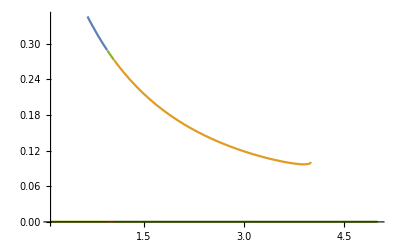

```mathematica
c:=4
p[x_,left_,right_]:=HeavisideTheta[x-left] HeavisideTheta[right-x]
Plot[{f1 p[x,0.1,0.95],f2 p[x,1.05,5],f3 p[x,0.95,1.05] },{x,0.1,5}]
```

```mathematica
FortranForm[f1]
```

```mathematica
(-2*c + ((2 - x**2)*Sqrt(c**2 - x**2))/(1 - x**2))/((1 + c)*x**2) + ((2 - 3*x**2)*ArcCosh((c + x**2)/((1 + c)*x)))/(x**2*(1 - x**2)**1.5) + (2*Log(((1 + c)*x)/(c + Sqrt(c**2 - x**2))))/x**2
```

(2 (1+c) Log x)/((c+Sqrt (c**2-x**2)) x**2)+(-2 c+(Sqrt (2-x**2) (c**2-x**2))/(1-x**2))/((1+c) x**2)+(ArcCosh (2-3 x**2) (c+x**2))/((1+c) x x**2 (1-x**2)**1.5)

```mathematica
FortranForm[f2]
```

(-2*c + ((2 - x**2)*Sqrt(c**2 - x**2))/(1 - x**2))/((1 + c)*x**2) - ((2 - 3*x**2)*ArcCos((c + x**2)/((1 + c)*x)))/(x**2*(-1 + x**2)**1.5) + (2*Log(((1 + c)*x)/(c + Sqrt(c**2 - x**2))))/x**2

```mathematica
FortranForm[f3]
```

(10*Sqrt(-1 + c**2) + c*(-6 - 6*c + 11*Sqrt(-1 + c**2)) + 6*(1 + c)**2*Log((1 + c)/(c + Sqrt(-1 + c**2))))/(3.*(1 + c)**2) + 
     -  (-1 + x)*((94 + c*(113 + 60*Sqrt((-1 + c)/(1 + c)) + 4*c*(-22 + 30*Sqrt((-1 + c)/(1 + c)) + c*(-26 + 15*Sqrt((-1 + c)/(1 + c))))))/(15.*(1 + c)**2*Sqrt(-1 + c**2)) - 4*Log(1 + c) + 
     -     4*Log(c + Sqrt(-1 + c**2)))

```mathematica
FullSimplify[Series[f1,{x,0,10}]]
```

(1/2+(413/640-3/4 Log[8/5]+(3 Log[x])/4) x^2+(49423/61440-5/4 Log[8/5]+(5 Log[x])/4) x^4+(497213/524288-105/64 Log[8/5]+(105 Log[x])/64) x^6+O[x]^7)+Floor[(π+Arg[x]-Arg[4+x^2])/(2 π)] ((4 ⅈ π)/x^2-3/2 ⅈ π x^2-5/2 ⅈ π x^4-105/32 ⅈ π x^6-63/16 ⅈ π x^8+O[x]^9)